# CAIM

Importar base de datos

```mathematica
data = SemanticImport[FileNameJoin[{NotebookDirectory[],"iris.data"}]]
```

Dataset[<>]

Cálculo de matriz quanta

```mathematica
DiscretizationCount[values_,discretizationScheme_]:=Block[{intervals,firstInterval,firstIntervalCount,restIntervals,restIntervalsCount},
intervals = Partition[discretizationScheme,2,1];

firstInterval = First[intervals];
firstIntervalCount = Count[values,x_/;First[firstInterval]≤x≤Last[firstInterval]];

restIntervals = Rest[intervals];
restIntervalsCount = Map[Count[values,x_/;First[#]<x≤Last[#]]&,restIntervals];

Return[Prepend[restIntervalsCount,firstIntervalCount]];
];

QuantaMatrix[values_,class_,discretizationScheme_]:=Block[{grouped,quantaMatrix},
grouped = GroupBy[Transpose[{values,class}],Last->First];
quantaMatrix = Map[DiscretizationCount[#,discretizationScheme]&,grouped];

<|
"QuantaMatrix"->quantaMatrix, 
"Values"->Values[quantaMatrix],
"ClassTotals"->Map[Total,Values[quantaMatrix]],
"IntervalTotals"->Map[Total,Transpose[Values[quantaMatrix]]]
|>
];

MaxR[m_,r_]:=Max[Part[Transpose[m],r]];

CAIMCriterion[quantaMatrix_]:=Block[{n},
n = Length[Transpose[quantaMatrix["Values"]]];

N[1/n*Sum[MaxR[quantaMatrix["Values"],r]^2/Part[quantaMatrix["IntervalTotals"],r],{r,n}]]
];

CAIMStep[values_,class_,discretizationScheme_]:=Block[{valuesAndMidpoints,BList,mutations,candidateDiscretizations},
valuesAndMidpoints = Sort[Join[values,Map[Mean,Partition[values,2,1]]]];
BList = DeleteCases[Sort[DeleteDuplicates[valuesAndMidpoints]],Apply[Alternatives,discretizationScheme]];
mutations = Map[Sort[Append[discretizationScheme,#]]&,BList];

candidateDiscretizations = Map[{#,Quiet@CAIMCriterion[QuantaMatrix[values,class,#]]}&,mutations];
candidateDiscretizations = DeleteCases[candidateDiscretizations,{_,Indeterminate}];

First[MaximalBy[candidateDiscretizations,Last]]
];
```

```mathematica
values = Normal@data[All,"Sepal length"];
```

```mathematica
class = Normal@data[All,"Class"];
```

```mathematica
scheme = MinMax[values]
```

{4.3,7.9}

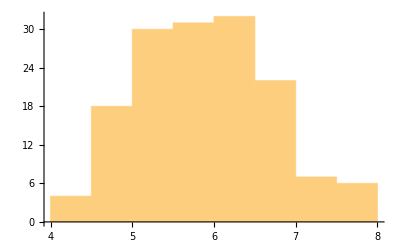

```mathematica
Histogram[values]
```

```mathematica
scheme
```

{4.3,7.9}

```mathematica
DiscretizationCount[values,scheme]
```

{150}

```mathematica
CAIMStep[values,class,scheme]
```

{{4.3,5.5,7.9},31.9126}

```mathematica
CAIMStep[values,class,{4.3,5.5,7.9}]
```

{{4.3,5.5,6.2,7.9},26.6363}

```mathematica
CAIMStep[values,class,{4.3,5.5,6.2,7.9}]
```

{{4.3,5.4,5.5,6.2,7.9},21.2455}

Algoritmo principal

```mathematica
CAIMAlgorithm[values_,class_,maxIterations_ :100]:=Block[{scheme,F,GlobalCAIM,k,CAIMScore,classes,caimResults},
scheme = MinMax[values];
classes = Length[DeleteDuplicates[class]];
F = Sort[values];
GlobalCAIM = 0;
CAIMScore = 0;
caimResults = {};

k = 1;
While[k<maxIterations,
{scheme,CAIMScore}= CAIMStep[values,class,scheme];
If[CAIMScore>GlobalCAIM|| k<classes,
AppendTo[caimResults,{scheme,CAIMScore}];
GlobalCAIM = CAIMScore;
,
Return[caimResults];
];
k++;
]
];

CAIMDiscretize[values_,class_]:=Block[{caimScheme,parts,discretizationRule},
caimScheme = First[Last[CAIMAlgorithm[values,class]]];
parts = Partition[caimScheme,2,1];

discretizationRule = MapIndexed[
If[First[#2] == 1,
x_ /; First[#1]≤x≤Last[#1]->First[#2]-1,
x_ /; First[#1]<x≤Last[#1]->First[#2]-1
]&,
parts
];

ReplaceAll[values, discretizationRule]
];

CAIMDatabaseDiscretize[database_]:=Block[{class,keys,discretized,discretizedRawDatabase},
class = Normal@database[All,"Class"];
keys = Keys[First[Normal[database]]];
discretized = Map[CAIMDiscretize[Normal@database[All,#],class]&,DeleteCases[keys,"Class"]];
discretizedRawDatabase = Transpose@Join[discretized,{Normal@database[All,"Class"]}];

Dataset[Map[Association[Thread[keys->#]]&,discretizedRawDatabase]]
];
```

```mathematica
CAIMAlgorithm[values,class]
```

{{{4.3,5.5,7.9},31.9126},{{4.3,5.5,6.2,7.9},26.6363}}

```mathematica
CAIMStep[values,class,{4.3,5.5,6.2,7.9}]
```

{{4.3,5.4,5.5,6.2,7.9},21.2455}

```mathematica
QuantaMatrix[values,class,{4.3,5.5,7.9}]
```

<|QuantaMatrix→<|Iris-setosa→{47,3},Iris-versicolor→{11,39},Iris-virginica→{1,49}|>,Values→{{47,3},{11,39},{1,49}},ClassTotals→{50,50,50},IntervalTotals→{59,91}|>

```mathematica
QuantaMatrix[values,class,{4.3,5.5,6.2,7.9}]
```

<|QuantaMatrix→<|Iris-setosa→{47,3,0},Iris-versicolor→{11,25,14},Iris-virginica→{1,12,37}|>,Values→{{47,3,0},{11,25,14},{1,12,37}},ClassTotals→{50,50,50},IntervalTotals→{59,40,51}|>

```mathematica
CAIMDiscretize[values,class]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,2,1,2,0,2,0,0,1,1,1,1,2,1,1,1,1,1,1,2,1,2,2,2,2,1,1,0,0,1,1,0,1,2,2,1,0,0,1,1,0,1,1,1,1,0,1,2,1,2,2,2,2,0,2,2,2,2,2,2,1,1,2,2,2,2,1,2,1,2,2,2,2,1,1,2,2,2,2,2,2,1,2,2,2,1,2,2,2,1,2,2,2,2,2,1,1}

```mathematica
CAIMDatabaseDiscretize[data]
```

Dataset[<>]